```mathematica
Unset[ϵ]
Vattr[ϵ_, r_,rc_,wc_] :=  ϵ  If [  r < rc,   -1, If [rc ≤ r ≤ rc+wc, - Cos[π * (r-rc)/(2*wc)]^2, 0]]
Vattr[ϵ,r,rc,wc]
```

ϵ If[r<rc,-1,If[rc≤r≤rc+wc,-Cos[(π (r-rc))/(2 wc)]^2,0]]

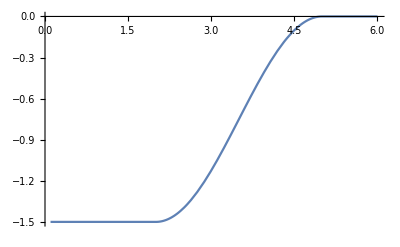

```mathematica
Plot[ Vattr[1.5,r, 2,3], {r, 0.1,6}]
```

```mathematica
Fattr[ϵ_,r_,rc_,wc_] :=- D[Vattr[ϵ, x,rc,wc],x] /. x->r
```

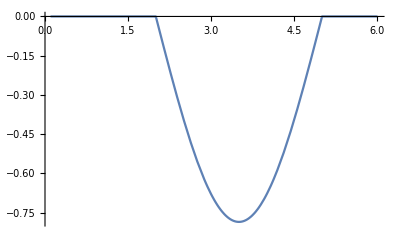

```mathematica
Plot[ Fattr[1.5,r, 2,3], {r, 0.1,6}]
```

```mathematica
Fattr[ϵ,r,rc,wc]
```

-ϵ If[r<rc,0,If[rc≤r≤rc+wc,(2 π Cos[(π (r-rc))/(2 wc)] Sin[(π (r-rc))/(2 wc)])/(2 wc),0]]

```mathematica
Vattr[2,3,2,3]/2 // N
Fattr[2,3,2,3] // N
```

-0.75

-0.9069